```mathematica
Grid[Table[Binomial[n,m],{n,0,10},{m,0,n}]]
```

1 |  |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  |  |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 |  |  | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 |  | 
1 | 9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 | 
1 | 10 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1

```mathematica
MatrixForm[Table[Binomial[n,m],{n,0,10},{m,0,n}]]
```

({1}
{1,1}
{1,2,1}
{1,3,3,1}
{1,4,6,4,1}
{1,5,10,10,5,1}
{1,6,15,20,15,6,1}
{1,7,21,35,35,21,7,1}
{1,8,28,56,70,56,28,8,1}
{1,9,36,84,126,126,84,36,9,1}
{1,10,45,120,210,252,210,120,45,10,1})

```mathematica
Mod[17,2]
```

1

```mathematica
Mod[10,2]
```

0

```mathematica
Grid[Table[Mod[Binomial[n,m],2],{n,0,10},{m,0,n}]]
```

1 |  |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  |  | 
1 | 0 | 1 |  |  |  |  |  |  |  | 
1 | 1 | 1 | 1 |  |  |  |  |  |  | 
1 | 0 | 0 | 0 | 1 |  |  |  |  |  | 
1 | 1 | 0 | 0 | 1 | 1 |  |  |  |  | 
1 | 0 | 1 | 0 | 1 | 0 | 1 |  |  |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | 
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 |  | 
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1

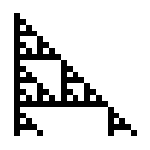

```mathematica
ArrayPlot[Table[Mod[Binomial[n,m],2],{n,0,20},{m,0,n}],ImageSize->150]
```

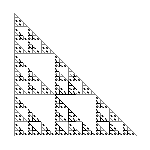

```mathematica
ArrayPlot[Table[Mod[Binomial[n,m],3],{n,0,3^5},{m,0,n}],ImageSize->150]
```

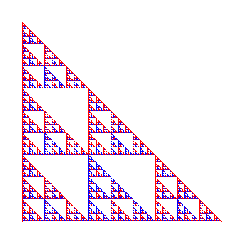

```mathematica
ArrayPlot[Table[Mod[Binomial[n,m],3],{n,0,3^5},{m,0,n}],ColorRules->{0->White,1->Red,2->Blue},Frame->None,PixelConstrained->1]
```

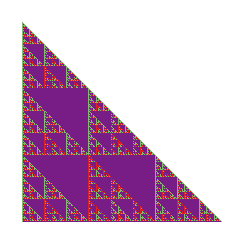

```mathematica
ArrayPlot[Table[Mod[Binomial[n,m],3],{n,0,3^5},{m,0,n}],ColorFunction->"Rainbow",Frame->None,PixelConstrained->1]
```

What about left-right symmetry?

```mathematica
Grid[Table[If[EvenQ[m],Binomial[n,m+Floor[n/2]],Null],{n,0,3^2},{m,-10,10}]]
```

0 |  | 0 |  | 0 |  | 0 |  | 0 |  | 1 |  | 0 |  | 0 |  | 0 |  | 0 |  | 0
0 |  | 0 |  | 0 |  | 0 |  | 0 |  | 1 |  | 0 |  | 0 |  | 0 |  | 0 |  | 0
0 |  | 0 |  | 0 |  | 0 |  | 0 |  | 2 |  | 0 |  | 0 |  | 0 |  | 0 |  | 0
0 |  | 0 |  | 0 |  | 0 |  | 0 |  | 3 |  | 1 |  | 0 |  | 0 |  | 0 |  | 0
0 |  | 0 |  | 0 |  | 0 |  | 1 |  | 6 |  | 1 |  | 0 |  | 0 |  | 0 |  | 0
0 |  | 0 |  | 0 |  | 0 |  | 1 |  | 10 |  | 5 |  | 0 |  | 0 |  | 0 |  | 0
0 |  | 0 |  | 0 |  | 0 |  | 6 |  | 20 |  | 6 |  | 0 |  | 0 |  | 0 |  | 0
0 |  | 0 |  | 0 |  | 0 |  | 7 |  | 35 |  | 21 |  | 1 |  | 0 |  | 0 |  | 0
0 |  | 0 |  | 0 |  | 1 |  | 28 |  | 70 |  | 28 |  | 1 |  | 0 |  | 0 |  | 0
0 |  | 0 |  | 0 |  | 1 |  | 36 |  | 126 |  | 84 |  | 9 |  | 0 |  | 0 |  | 0

```mathematica
?Riffle
```

Riffle[{e_1,e_2,…},x] gives {e_1,x,e_2,x,…}. 
Riffle[{e_1,e_2,…},{x_1,x_2,…}] gives {e_1,x_1,e_2,x_2,…}. 
Riffle[list,x,n] yields a list in which every n^th element is x. 
Riffle[list,x,{i_min,i_max,n}] yields a list in which x appears if possible at positions i_min, i_min+n, i_min+2n, … , i_max.

```mathematica
Riffle[{1,4,6,4,1},x]
```

{1,x,4,x,6,x,4,x,1}

```mathematica
ConstantArray[x,10]
```

{x,x,x,x,x,x,x,x,x,x}

```mathematica
Module[{maxn=15},Grid[Table[Join[ConstantArray[Null,maxn-n],Riffle[Table[Binomial[n,m],{m,0,n}],Null]],{n,0,maxn}],ItemSize->All]]
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 2 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 3 |  | 3 |  | 1 |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  | 1 |  | 4 |  | 6 |  | 4 |  | 1 |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  | 1 |  | 5 |  | 10 |  | 10 |  | 5 |  | 1 |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  | 1 |  | 6 |  | 15 |  | 20 |  | 15 |  | 6 |  | 1 |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 1 |  | 7 |  | 21 |  | 35 |  | 35 |  | 21 |  | 7 |  | 1 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 1 |  | 8 |  | 28 |  | 56 |  | 70 |  | 56 |  | 28 |  | 8 |  | 1 |  |  |  |  |  |  | 
 |  |  |  |  |  | 1 |  | 9 |  | 36 |  | 84 |  | 126 |  | 126 |  | 84 |  | 36 |  | 9 |  | 1 |  |  |  |  |  | 
 |  |  |  |  | 1 |  | 10 |  | 45 |  | 120 |  | 210 |  | 252 |  | 210 |  | 120 |  | 45 |  | 10 |  | 1 |  |  |  |  | 
 |  |  |  | 1 |  | 11 |  | 55 |  | 165 |  | 330 |  | 462 |  | 462 |  | 330 |  | 165 |  | 55 |  | 11 |  | 1 |  |  |  | 
 |  |  | 1 |  | 12 |  | 66 |  | 220 |  | 495 |  | 792 |  | 924 |  | 792 |  | 495 |  | 220 |  | 66 |  | 12 |  | 1 |  |  | 
 |  | 1 |  | 13 |  | 78 |  | 286 |  | 715 |  | 1287 |  | 1716 |  | 1716 |  | 1287 |  | 715 |  | 286 |  | 78 |  | 13 |  | 1 |  | 
 | 1 |  | 14 |  | 91 |  | 364 |  | 1001 |  | 2002 |  | 3003 |  | 3432 |  | 3003 |  | 2002 |  | 1001 |  | 364 |  | 91 |  | 14 |  | 1 | 
1 |  | 15 |  | 105 |  | 455 |  | 1365 |  | 3003 |  | 5005 |  | 6435 |  | 6435 |  | 5005 |  | 3003 |  | 1365 |  | 455 |  | 105 |  | 15 |  | 1

```mathematica
Module[{maxn=15},ArrayPlot[Table[Join[ConstantArray[0,maxn-n],Riffle[Table[Mod[Binomial[n,m],2],{m,0,n}],0]],{n,0,maxn}],Frame->None,PixelConstrained->4]]
```

-Graphics-

```mathematica
Module[{maxn=15},ArrayPlot[Table[Join[
ConstantArray[Null,maxn-n],Riffle[Table[Mod[Binomial[n,m],2],{m,0,n}],Null],
ConstantArray[Null,maxn-n]
],{n,0,maxn}],ColorRules->{Null->White,0->Red,1->Blue},Frame->None,PixelConstrained->4]]
```

-Graphics-

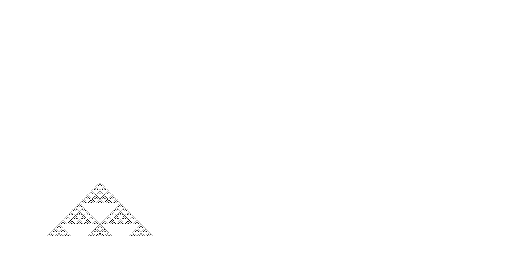

```mathematica
Module[{maxn=2^6},ArrayPlot[Table[Join[ConstantArray[0,maxn-n],Riffle[Table[Mod[Binomial[n,m],5],{m,0,n}],0]],{n,0,maxn}],Frame->None,PixelConstrained->4]]
```

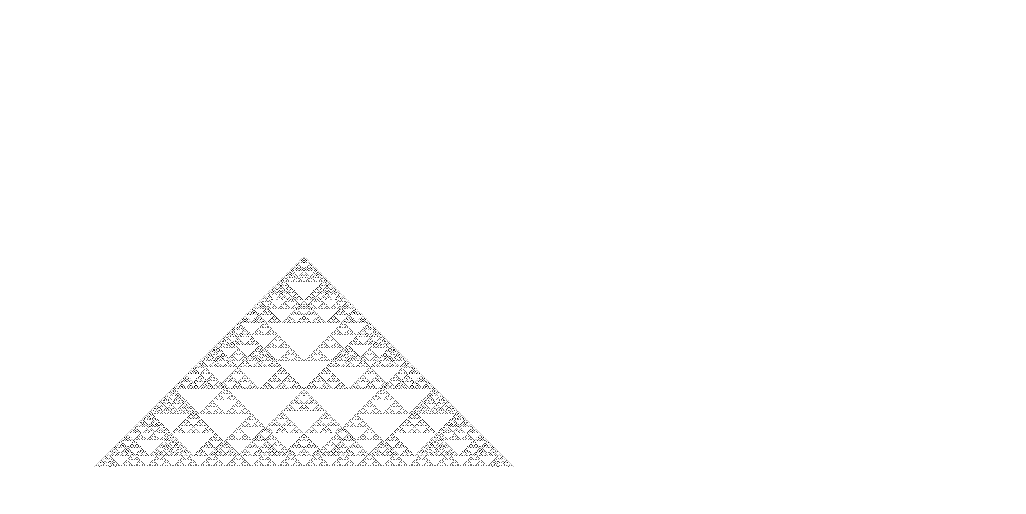

```mathematica
Module[{maxn=2^8,null=0},ArrayPlot[Table[Join[ConstantArray[null,maxn-n],Riffle[Table[Mod[Binomial[n,m],6],{m,0,n}],null]],{n,0,maxn}],Frame->None,PixelConstrained->2]]
```

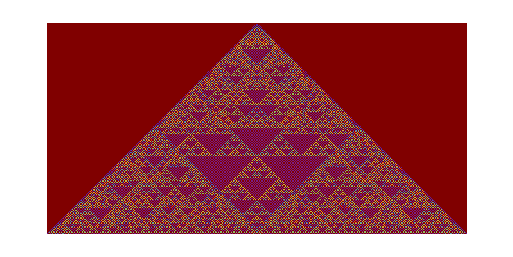

```mathematica
Module[{maxn=2^8,null=Null},ArrayPlot[Table[Join[ConstantArray[null,maxn-n],Riffle[Table[Mod[Binomial[n,m],30],{m,0,n}],null],ConstantArray[null,maxn-n]],{n,0,maxn}],ColorFunction->"Rainbow",Frame->None,PixelConstrained->1]]
```

```mathematica
Module[{maxn=2^8,null=Null},ArrayPlot[Table[Join[ConstantArray[null,maxn-n],Riffle[Table[Mod[Binomial[n,m],30],{m,0,n}],null],ConstantArray[null,maxn-n]],{n,0,maxn}],ColorFunction->"Rainbow",Frame->None,PixelConstrained->2]]
```

## guessing a sequence

How many ways are there to balance n pairs of parentheses?

```mathematica
[[[[
```

One pair:

```mathematica
[]
```

Two pairs:

```mathematica
[][]
```

```mathematica
[[]]
```

Three pairs:

```mathematica
[][][]
[[]][]
[][[]]
[[[]]]
[[][]]
```

```mathematica
{0,1,0,1,0,1}
{0,0,1,1,0,1}
```

```mathematica
Table[IntegerDigits[n,2],{n,9,15}]
```

{{1,0,0,1},{1,0,1,0},{1,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,1,0},{1,1,1,1}}

```mathematica
?Tuples
```

Tuples[list,n] generates a list of all possible n-tuples of elements from list. 
Tuples[{list_1,list_2,…}] generates a list of all possible tuples whose i^th element is from list_i.

```mathematica
Tuples[{0,1},4]
```

{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0},{1,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,1,0},{1,1,1,1}}

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

```mathematica
Select[{1,2,3,4},EvenQ]
```

{2,4}

```mathematica
Select[Tuples[{0,1},4],Function[tuple,First[tuple]==0&&Last[tuple]==1]]
```

{{0,0,0,1},{0,0,1,1},{0,1,0,1},{0,1,1,1}}

```mathematica
Module[{n=2},Select[Tuples[{0,1},2n],Function[tuple,First[tuple]==0&&Last[tuple]==1&&Total[tuple]==n]]]
```

{{0,0,1,1},{0,1,0,1}}

```mathematica
Module[{n=3},Select[Tuples[{0,1},2n],Function[tuple,First[tuple]==0&&Last[tuple]==1&&Total[tuple]==n]]]
```

{{0,0,0,1,1,1},{0,0,1,0,1,1},{0,0,1,1,0,1},{0,1,0,0,1,1},{0,1,0,1,0,1},{0,1,1,0,0,1}}

```mathematica
[]][[]
```

```mathematica
Module[{n=3},Select[Tuples[{-1,1},2n],Function[tuple,First[tuple]==-1&&Last[tuple]==1&&Total[tuple]==0]]]
```

{{-1,-1,-1,1,1,1},{-1,-1,1,-1,1,1},{-1,-1,1,1,-1,1},{-1,1,-1,-1,1,1},{-1,1,-1,1,-1,1},{-1,1,1,-1,-1,1}}

```mathematica
?Accumulate
```

Accumulate[list] gives a list of the successive accumulated totals of elements in list.

```mathematica
Accumulate[{-1,1,1,-1,-1,1}]
```

{-1,0,1,0,-1,0}

```mathematica
Max[{-1,0,1,0,-1,0}]
```

1

```mathematica
?MemberQ
```

MemberQ[list,form] returns True if an element of list matches form, and False otherwise. 
MemberQ[list,form,levelspec] tests all parts of list specified by levelspec.

```mathematica
Module[{n=3},Select[Tuples[{-1,1},2n],Function[tuple,First[tuple]==-1&&Last[tuple]==1&&Total[tuple]==0&&!MemberQ[Accumulate[tuple],1]]]]
```

{{-1,-1,-1,1,1,1},{-1,-1,1,-1,1,1},{-1,-1,1,1,-1,1},{-1,1,-1,-1,1,1},{-1,1,-1,1,-1,1}}

```mathematica
BracketCount[n_]:=Length[Select[Tuples[{-1,1},2n],Function[tuple,First[tuple]==-1&&Last[tuple]==1&&Total[tuple]==0&&!MemberQ[Accumulate[tuple],1]]]]
```

```mathematica
BracketCount[3]
```

5

```mathematica
Table[BracketCount[n],{n,0,4}]
```

First::first: {} has a length of zero and no first element.

Last::nolast: {} has a length of zero and no last element.

{0,1,2,5,14}

```mathematica
Table[BracketCount[n],{n,1,9}]
```

{1,2,5,14,42,132,429,1430,4862}

```mathematica
BracketCount2[n_]:=Length[Select[Tuples[{-1,1},2n],Function[tuple,Total[tuple]==0&&!MemberQ[Accumulate[tuple],1]]]]
```

```mathematica
Table[BracketCount2[n],{n,0,9}]
```

{1,1,2,5,14,42,132,429,1430,4862}

```mathematica
?TimeConstrained
```

TimeConstrained[expr,t] evaluates expr, stopping after t seconds. 
TimeConstrained[expr,t,failexpr] returns failexpr if the time constraint is not met.

```mathematica
TimeConstrained[Do[Print[{n,BracketCount2[n]}],{n,0,20}],10]
```

{0,1}

{1,1}

{2,2}

{3,5}

{4,14}

{5,42}

{6,132}

{7,429}

{8,1430}

{9,4862}

{10,16796}

$Aborted

```mathematica
CatalanNumber[Range[0,20]]
```

{1,1,2,5,14,42,132,429,1430,4862,16796,58786,208012,742900,2674440,9694845,35357670,129644790,477638700,1767263190,6564120420}

```mathematica
Attributes[CatalanNumber]
```

{Listable,NumericFunction,Protected,ReadProtected}

## Catalan numbers modulo 2

```mathematica
Mod[CatalanNumber[Range[0,20]],2]
```

{1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0}

```mathematica
Select[Range[0,1000],Function[n,OddQ[CatalanNumber[n]]]]
```

{0,1,3,7,15,31,63,127,255,511}

```mathematica
?Log
```

Log[z] gives the natural logarithm of z (logarithm to base e). 
Log[b,z] gives the logarithm to base b.

```mathematica
Log[2,2^7]
```

7

```mathematica
?IntegerQ
```

IntegerQ[expr] gives True if expr is an integer, and False otherwise.

```mathematica
Log[2,40]
```

Log[40]/Log[2]

```mathematica
2^6-1
```

```mathematica
IntegerQ[Log[2,63+1]]
```

True

```mathematica
Table[If[IntegerQ[Log[2,n+1]],1,0],{n,0,20}]
```

{1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0}

```mathematica
Table[Mod[CatalanNumber[n],2],{n,0,20}]
```

{1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0}

```mathematica
DeleteDuplicates[Table[If[IntegerQ[Log[2,n+1]],1,0]==Mod[CatalanNumber[n],2],{n,0,10000}]]
```

{True}

Conjecture.  The nth Catalan number is odd if and only if n==2^a-1.

```mathematica
DeleteDuplicates[Table[CatalanNumber[n]==Binomial[2n,n]/(n+1),{n,0,1000}]]
```

{True}

```mathematica
IntegerExponent[CatalanNumber[n],2]
```

```mathematica
IntegerExponent[Binomial[2 n,n]/(n+1),2]
```

```mathematica
IntegerExponent[((2n)!)/((n!)^2(n+1)),2]
```

```mathematica
IntegerExponent[(2n)!,2]-2IntegerExponent[n!,2]-IntegerExponent[n+1,2]
```

Use this formula for ⋁_p (n!):

```mathematica
IntegerExponent[n!,p]==(n-Total[IntegerDigits[n,p]])/(p-1)
```

```mathematica
(2n-Total[IntegerDigits[2n,2]])/(2-1)-2(n-Total[IntegerDigits[n,2]])/(2-1)-IntegerExponent[n+1,2]
```

```mathematica
2n-Total[IntegerDigits[2n,2]]-2n+2Total[IntegerDigits[n,2]]-IntegerExponent[n+1,2]
```

```mathematica
-Total[IntegerDigits[n,2]]+2Total[IntegerDigits[n,2]]-IntegerExponent[n+1,2]
```

```mathematica
Total[IntegerDigits[n,2]]-IntegerExponent[n+1,2]
```

```mathematica
DeleteDuplicates[Table[Total[IntegerDigits[n,2]]-IntegerExponent[n+1,2]==IntegerExponent[CatalanNumber[n],2],{n,0,1000}]]
```

{True}

If n==2^a-1:

```mathematica
Total[IntegerDigits[2^a-1,2]]-IntegerExponent[2^a-1+1,2]
```

```mathematica
Total[IntegerDigits[2^a-1,2]]-IntegerExponent[2^a,2]
```

```mathematica
Total[IntegerDigits[2^a-1,2]]-a
```

```mathematica
a-a
```

0

If ν_2(C(n))==0:

```mathematica
Total[IntegerDigits[n,2]]-IntegerExponent[n+1,2]==0
```

```mathematica
Total[IntegerDigits[n,2]]==IntegerExponent[n+1,2]
```

Homework:  Finish the proof.

## Catalan numbers modulo 4

```mathematica
Table[Mod[CatalanNumber[n],4],{n,0,100}]
```

{1,1,2,1,2,2,0,1,2,2,0,2,0,0,0,1,2,2,0,2,0,0,0,2,0,0,0,0,0,0,0,1,2,2,0,2,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,2,0,2,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0}

```mathematica
DeleteDuplicates[Table[Mod[CatalanNumber[n],4],{n,0,10000}]]
```

{1,2,0}

Conjecture.  No Catalan number is congruent to 3 modulo 4.

Conjecture.  For n≥2, if C(n)≡1 mod 4 then C(n+1)≡C(n+2)≡2 mod 4.

Where is the nth Catalan number congruent to 1 mod 4?
Assuming that there are no 3’s, it’s the same:

```mathematica
Select[Range[0,1000],Function[n,OddQ[CatalanNumber[n]]]]
```

{0,1,3,7,15,31,63,127,255,511}

Without any assumption...

```mathematica
Select[Range[0,1000],Function[n,Mod[CatalanNumber[n],4]==1]]
```

{0,1,3,7,15,31,63,127,255,511}

```mathematica
Select[Range[0,1000],Function[n,Mod[CatalanNumber[n],4]==2]]
```

{2,4,5,8,9,11,16,17,19,23,32,33,35,39,47,64,65,67,71,79,95,128,129,131,135,143,159,191,256,257,259,263,271,287,319,383,512,513,515,519,527,543,575,639,767}

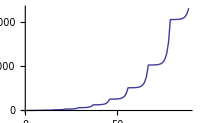

```mathematica
ListLinePlot[Select[Range[0,10000],Function[n,Mod[CatalanNumber[n],4]==2]],ImageSize->200]
```

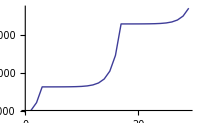

```mathematica
ListLinePlot[Select[Range[10000,40000],Function[n,Mod[CatalanNumber[n],4]==2]],ImageSize->200]
```

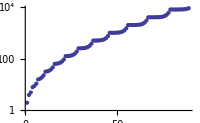

```mathematica
ListLogPlot[Select[Range[0,10000],Function[n,Mod[CatalanNumber[n],4]==2]],ImageSize->200]
```

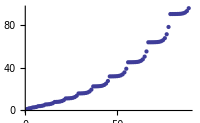

```mathematica
ListPlot[Sqrt[Select[Range[0,10000],Function[n,Mod[CatalanNumber[n],4]==2]]],ImageSize->200]
```

```mathematica
Table[IntegerExponent[5n^2+4n+4,2],{n,1,100}]
```

{0,5,0,2,0,4,0,2,0,5,0,2,0,4,0,2,0,5,0,2,0,4,0,2,0,5,0,2,0,4,0,2,0,5,0,2,0,4,0,2,0,5,0,2,0,4,0,2,0,5,0,2,0,4,0,2,0,5,0,2,0,4,0,2,0,5,0,2,0,4,0,2,0,5,0,2,0,4,0,2,0,5,0,2,0,4,0,2,0,5,0,2,0,4,0,2,0,5,0,2}

```mathematica
Table[IntegerExponent[n,2],{n,1,100}]
```

{0,1,0,2,0,1,0,3,0,1,0,2,0,1,0,4,0,1,0,2,0,1,0,3,0,1,0,2,0,1,0,5,0,1,0,2,0,1,0,3,0,1,0,2,0,1,0,4,0,1,0,2,0,1,0,3,0,1,0,2,0,1,0,6,0,1,0,2,0,1,0,3,0,1,0,2,0,1,0,4,0,1,0,2,0,1,0,3,0,1,0,2,0,1,0,5,0,1,0,2}

Create the tree for Catalan numbers modulo 4:

```mathematica
Table[Mod[CatalanNumber[n],4],{n,0,100}]
```

{1,1,2,1,2,2,0,1,2,2,0,2,0,0,0,1,2,2,0,2,0,0,0,2,0,0,0,0,0,0,0,1,2,2,0,2,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,2,0,2,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0}

```mathematica
Table[Mod[CatalanNumber[n],4],{n,0,100}]
```